SWAP Test

Quantum Circuitpaclet:QuantumMob/Q3S/tutorial/SWAPTest#803320025 | Notespaclet:QuantumMob/Q3S/tutorial/SWAPTest#365092346
Demonstrationpaclet:QuantumMob/Q3S/tutorial/SWAPTest#678204349 |

The swap test is a quantum computing procedure used to compare the quantum states of two quantum registers indirectly. It is commonly used in quantum machine learning, quantum search, and quantum state estimation.

Fredkinpaclet:QuantumMob/Q3S/ref/FredkinQuantumMob Package Symbol | The Fredkin or controlled-swap gate.
Hadarmardpaclet:QuantumMob/Q3S/ref/HadarmardQuantumMob Package Symbol | The Hadamard gate.
ProductStatepaclet:QuantumMob/Q3S/ref/ProductStateQuantumMob Package Symbol | The product state.

Quantum circuit elements used to implement the swap test.

Quantum Circuit

Figure 1 below shows a quantum circuit for the swap test.

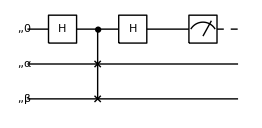

Figure 1. A quantum circuit for the SWAP test. The first quantum register is a single qubit whereas the second and third quantum registers consist of an equal number of qubits.

The first Hadamard gate and the controlled-swap gate (also known as the Fredkin gate for single-qubit target registers) converts the initial state to

0⊗a,β↦(0+1)⊗a,β↦0⊗a,β+1⊗β,α .

Then, the second Hadamard gate on the control qubit leads to

(0+1)⊗a,β+(0-1)⊗β,α⊗α=0⊗(α,β+β,α)+1⊗(α,β-β,α) .

Therefore, upon the measurement on the control qubit, the probability for measurement outcomes 0 and 1 are given by

P_0=1/2+1/2(|αβ|)^2

and

P_1=1/2-1/2(|αβ|)^2 ,

respectively.

Demonstration

```mathematica
Needs["QuamtumMob`Q3`"]
```

```mathematica
Let[Qubit,S,T]
Let[Complex,c]
```

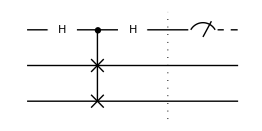

```mathematica
qc=QuantumCircuit[Ket[{S}],
ProductState[T[1]->c[1,{0,1}],"Label"->Ket[α]],
ProductState[T[2]->c[2,{0,1}],"Label"->Ket[β]],
S[6],Fredkin[S,T@{1,2}],S[6]
];
test=QuantumCircuit[qc,"Separator",Measurement[S[3]]]
```

```mathematica
SeedRandom[366];
```

```mathematica
out=Elaborate[qc]
```

c_(,,10) c_(,,20) 0_(,,S)0_(,,T_(,,1))0_(,,T_(,,2))+1/2 (c_(,,11) c_(,,20)+c_(,,10) c_(,,21)) 0_(,,S)0_(,,T_(,,1))1_(,,T_(,,2))+1/2 (c_(,,11) c_(,,20)+c_(,,10) c_(,,21)) 0_(,,S)1_(,,T_(,,1))0_(,,T_(,,2))+c_(,,11) c_(,,21) 0_(,,S)1_(,,T_(,,1))1_(,,T_(,,2))+1/2 (-c_(,,11) c_(,,20)+c_(,,10) c_(,,21)) 1_(,,S)0_(,,T_(,,1))1_(,,T_(,,2))+1/2 (c_(,,11) c_(,,20)-c_(,,10) c_(,,21)) 1_(,,S)1_(,,T_(,,1))0_(,,T_(,,2))

Notes

In the simple method introduced above, one can get the absolute value of the Hermitian product. It is also possible to get the sign (for real vectors) or real part (for complex vectors) as well. See Section 6.1.1 of Schult and Petruccione (2018) and Zhao, Fitzsimons and Fitzsimons (2019).

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪M. Schult and F. Petruccione (2018)https://doi.org/10.1007/978-3-319-96424-9, "Supervised Learning with Quantum Computers" (Springer).
▪Z. Zhao, J. K. Fitzsimons, and J. F. Fitzsimons (2019)https://doi.org/10.1103/physreva.99.052331, Physical Review A 99, 052331 (2019), "Quantum-assisted Gaussian process regression."
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).